```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[{Plot,ListPlot},BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->12]];
```

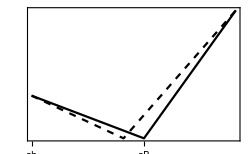

```mathematica
ListPlot[
{
{{0,0.5},{1.1,0},{2,1.5}},
{{0,0.5},{0.9,0},{2,1.5}}
},
Joined->True,Axes->False,Frame->True,FrameTicks->{{None,{{0,"1-δ"},{0.5,"1"},{1.5,"1+s"}}},{{{0,"ab"},{0.9,"Ab"},{1.1,"aB"},{2,"AB"}},None}},
FrameTicksStyle->Black,
PlotStyle->{Directive[Black],Directive[Black,Dashed]},
ImageSize->250]
```

```mathematica
Export["../ms/Figures/valley.pdf",%];
```